```mathematica
SetDirectory[NotebookDirectory[]];
<<Functions`

tol=10^(-6);
```

```mathematica
(*define the evolving domain:*)
M=9;
cols=Table[ColorData["Rainbow"][(i-1)/M],{i,1,M}];
```

```mathematica
cp1={{-0.5,7.5,0.5},{0,6,1}};
cp2={{0.5,7.5,0.5},{0,6,1}};
cp3={{0,6,1}};
cp4={{0,6,1},{0,3,1}};
cp5={{0,3,1}};
cp6={{0,3,1}};
cp7={{0,3,1}};
cp8={{0,3,1}};
cp9={{0,3,1}};
cps={cp1,cp2,cp3,cp4,cp5,cp6,cp7,cp8,cp9};
cps0=Table[Table[cps[[m,i]]+{0,0,0},{i,1,Length@cps[[m]]}],{m,1,M}];
mas0=Table[BCurve[cps0[[m]],u],{m,1,M}];
objs0=Table[Env[mas0[[m]],u,tol],{m,1,M}];

cp1={{-1,9,0.7},{-0.5,8,0.8},{-0.25,6.8,0.9},{0,6,1}};
cp2={{1,9,0.7},{0.5,7.25,0.8},{0.25,6.7,0.9},{0,6,1}};
cp3={{0,6,1}};
cp4={{0,6,1},{1,3,3}};
cp5={{1,3,3},{0,1,1}};
cp6={{1,3,3},{2.6,3,2.6},{4,2.6,2.3}};
cp7={{4,2.6,2.3}};
cp8={{4,2.6,2.3}};
cp9={{4,2.6,2.3}};
cps={cp1,cp2,cp3,cp4,cp5,cp6,cp7,cp8,cp9};
cps1=Table[Table[cps[[m,i]]+{10,0,0},{i,1,Length@cps[[m]]}],{m,1,M}];
mas1=Table[BCurve[cps1[[m]],u],{m,1,M}];
objs1=Table[Env[mas1[[m]],u,tol],{m,1,M}];

cp1={{0.5,9,0.25},{0.6,7.8,0.35},{0.8,6.8,0.2},{1.32,6,1}};
cp2={{2.8,8.6,0.35},{2,7.25,0.35},{1.7,6.7,0.3},{1.32,6,1}};
cp3={{0.2,5.8,0.6},{0.8,5.9,0.8},{1.32,6,1}};
cp4={{1.32,6,1},{2.6,3,2.6}};
cp5={{2.6,3,2.6},{2,1,1},{1,0,0.5}};
cp6={{2.6,3,2.6},{4,2.6,2.3}};
cp7={{4,2.6,2.3},{4.4,1,1}};
cp8={{4,2.6,2.3},{5,1.5,1.1}};
cp9={{4,2.6,2.3},{5.28,3.4,1}};
cps={cp1,cp2,cp3,cp4,cp5,cp6,cp7,cp8,cp9};
cps2=Table[Table[cps[[m,i]]+{20,0,0},{i,1,Length@cps[[m]]}],{m,1,M}];
mas2=Table[BCurve[cps2[[m]],u],{m,1,M}];
objs2=Table[Env[mas2[[m]],u,tol],{m,1,M}];

cp1={{0.5,9,0.25},{0.6,7.8,0.35},{0.8,6.8,0.2},{1.32,6,1}};
cp2={{2.8,8.6,0.35},{2,7.25,0.35},{1.7,6.7,0.3},{1.32,6,1}};
cp3={{0.2,5.8,0.6},{0.8,5.9,0.8},{1.32,6,1}};
cp4={{1.32,6,1},{1.8,4.3,1.5},{2.6,3,2.6}};
cp5={{2.6,3,2.6},{2,1,1},{1,0,0.5},{0,0,0.3}};
cp6={{2.6,3,2.6},{4,2.6,2.3}};
cp7={{4,2.6,2.3},{4.4,1,1},{5.2,0.3,0.6},{3.7,0,0.2}};
cp8={{4,2.6,2.3},{5,1.5,1.1},{6.2,1.4,0.6}};
cp9={{4,2.6,2.3},{5.28,3.4,1},{5.6,3.8,0.5}};
cps={cp1,cp2,cp3,cp4,cp5,cp6,cp7,cp8,cp9};
cps3=Table[Table[cps[[m,i]]+{30,0,0},{i,1,Length@cps[[m]]}],{m,1,M}];
mas3=Table[BCurve[cps3[[m]],u],{m,1,M}];
objs3=Table[Env[mas3[[m]],u,tol],{m,1,M}];

(*control points*)
cps=Table[{cps0[[m]],cps1[[m]],cps2[[m]],cps3[[m]]},{m,1,M}];
idx=Table[i,{i,0,1,0.01}];
parO={0.,0.25,0.5,0.75,1.};
idxO=Flatten@Table[Position[idx,parO[[i]]][[1]],{i,1,Length@parO}];
ts=idx;
us=Table[i,{i,0,1,0.5}];

(*surface for every branch*)
surfs=Table[BSurf[Table[cps[[m,i]],{i,1,Length@cps[[m]]}],t,u],{m,1,M}];
mas=Table[Table[surfs[[m]]/.{t->T},{T,idx}],{m,1,M}];
objs=Table[Table[Env[mas[[m,i]],u,tol],{i,idxO}],{m,1,M}];
CS=Table[Table[Table[mas[[m,i]]/.{u->j},{j,0,1,1/50}],{i,1,Length@mas[[m]]}],{m,1,M}];

sh0=Show[
Table[Table[Table[Graphics[{LightBlue,Disk[CS[[m,i,j,1;;2]],Abs@CS[[m,i,j,3]]]}],{j,1,Length@CS[[m,i]]}],{i,1,Length@CS[[m]]}],{m,1,M}],
Table[Table[ParametricPlot[objs[[m,i]],{u,0,1},PlotStyle->{Thick,cols[[m]]}],{i,1,Length@idxO}],{m,1,M}],
Table[Table[Graphics[{Thick,cols[[m]],Circle[CS[[m,i,-1,1;;2]],Abs@CS[[m,i,-1,3]]]}],{i,idxO}],{m,1,M}],
Table[Table[Graphics[{Thick,cols[[m]],Circle[CS[[m,i,1,1;;2]],Abs@CS[[m,i,1,3]]]}],{i,idxO}],{m,1,M}],
Table[Table[Table[Graphics[{LightBlue,Disk[CS[[m,i,j,1;;2]],Abs@CS[[m,i,j,3]]]}],{j,1,Length@CS[[m,i]]}],{i,idxO}],{m,1,M}],
Table[Table[Table[Graphics[{Thin,cols[[m]],Circle[mas[[m,i,1;;2]]/.{u->U},Abs[mas[[m,i,3]]/.{u->U}]]}],{U,0,1,0.5}],{i,idxO}],{m,1,M}],Table[Table[ParametricPlot[mas[[m,i,1;;2]],{u,0,1},PlotStyle->{cols[[m]]}],{i,idxO}],{m,1,M}],
PlotRange->All,Frame->True,FrameTicks->None,Axes->False,LabelStyle->Tiny]

sh1=Show[
Table[Table[Table[Graphics[{LightBlue,Disk[CS[[m,i,j,1;;2]],Abs@CS[[m,i,j,3]]]}],{j,1,Length@CS[[m,i]]}],{i,1,Length@CS[[m]]}],{m,1,M}],
PlotRange->All,Frame->True,FrameTicks->None,Axes->False,LabelStyle->Tiny];
```

-Graphics-

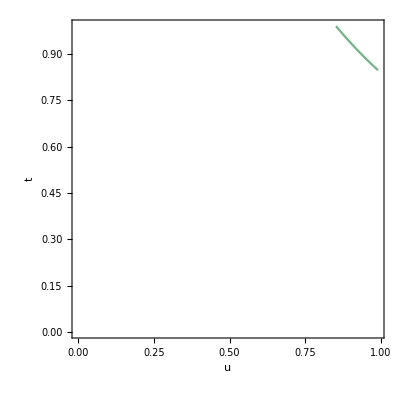
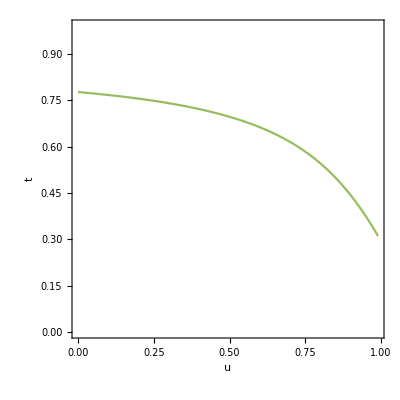
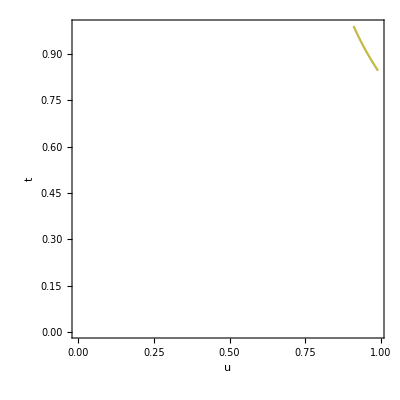
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*singular curves*)
dets=Table[Factor@Det[(({D[surfs[[m]],u],D[surfs[[m]],t]}).MSignatureMat).Transpose[{D[surfs[[m]],u],D[surfs[[m]],t]}]],{m,1,M}];
sh2=Table[ContourPlot[dets[[m]]==0,{u,0,0.99},{t,0,0.99},PlotPoints->50,ContourStyle->cols[[m]],FrameLabel->Automatic,RotateLabel->False,LabelStyle->Medium],{m,1,M}]
```

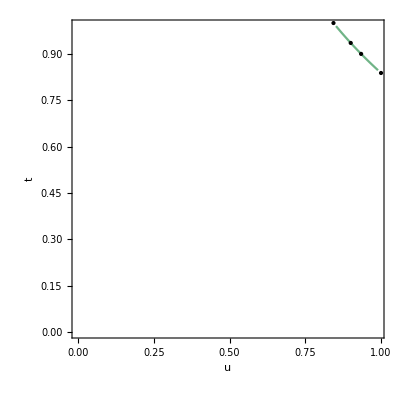
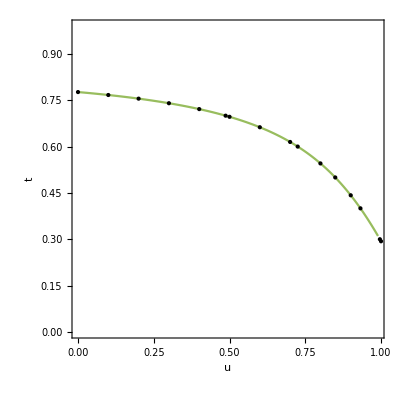
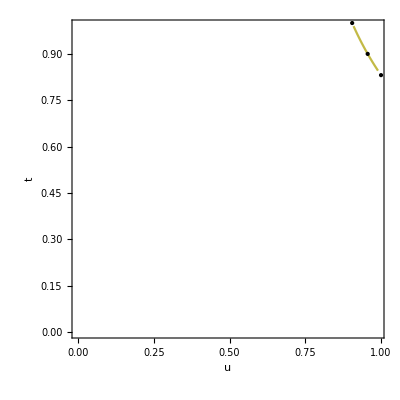

```mathematica
gridstep=0.1;

MM={5,6,7}; (*just the branches that contain a singular curve*)

(*get points on the singular curves*)
uEqs=Table[Table[Simplify[dets[[m]]/.{t->i}],{i,0,1,gridstep}],{m,MM}];
tEqs=Table[Table[Simplify[dets[[m]]/.{u->i}],{i,0,1,gridstep}],{m,MM}];

uPars=Table[Table[Table[Newton[uEqs[[m,i]],u,j,tol,100],{i,1,Length@uEqs[[m]]}],{m,1,Length@uEqs}],{j,0,1,gridstep}];
uPtsA=Table[Table[DeleteCases[Table[If[uPars[[j]][[m,i,1]]==1&&uPars[[j]][[m,i,3]]<tol&&tol<uPars[[j]][[m,i,2]]<1,{uPars[[j]][[m,i,2]],(i-1)*gridstep},{}],{i,1,Length@uPars[[j]][[m]]}],{}],{m,1,Length@uPars[[j]]}],{j,1,Length@uPars}];
uPts=Table[DeleteDuplicates[Flatten[uPtsA[[All,m]],1],Norm[#1-#2]<tol&],{m,1,Length@uPtsA[[1]]}];

tPars=Table[Table[Table[Newton[tEqs[[m,i]],t,j,tol,500],{i,1,Length@tEqs[[m]]}],{m,1,Length@tEqs}],{j,0,1,gridstep}];
tPtsA=Table[Table[DeleteCases[Table[If[tPars[[j]][[m,i,1]]==1&&tPars[[j]][[m,i,3]]<tol&&tol<tPars[[j]][[m,i,2]]<1,{(i-1)*gridstep,tPars[[j]][[m,i,2]]},{}],{i,1,Length@tPars[[j]][[m]]}],{}],{m,1,Length@tPars[[j]]}],{j,1,Length@tPars}];
tPts=Table[DeleteDuplicates[Flatten[tPtsA[[All,m]],1],Norm[#1-#2]<tol&],{m,1,Length@tPtsA[[1]]}];

sh4=Table[Show[sh2[[MM[[i]]]],
Graphics[{Point[uPts[[i]]]}],
Graphics[{Point[tPts[[i]]]}]
],{i,1,Length@MM}]
```

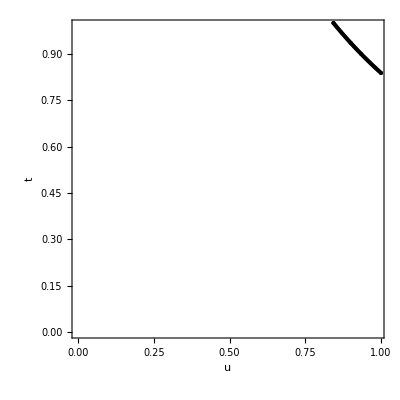
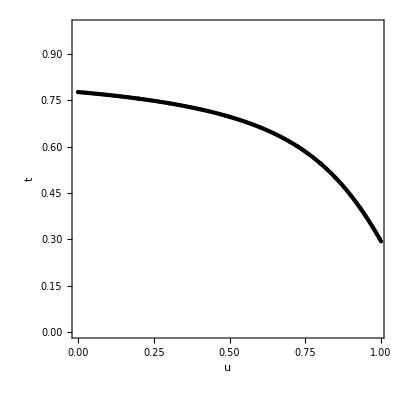
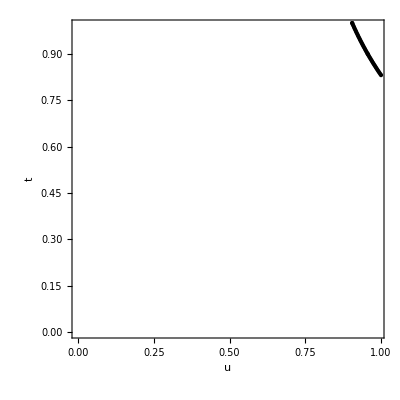

```mathematica
(*trace the singular curves*)
startingPoints1=Table[SortBy[Join[uPts[[m]],tPts[[m]]],{#[[1]],#[[2]]}&],{m,1,Length@MM}];

pts=Table[{},{m,1,Length@MM}];
predictStep=0.005;

Table[(While[Length@startingPoints1[[mm]]>0,(
branch=1;
pt=startingPoints1[[mm,1]];
branchPts={};
it=0;
While[it<1000&&0<=pt[[1]]<=1&&0<=pt[[2]]<=1,(
branchPts=Join[branchPts,{pt}];
tgVec={{0,-1},{1,0}}.Normalize[{D[dets[[MM[[mm]]]],u],D[dets[[MM[[mm]]]],t]}/.{u->pt[[1]],t->pt[[2]]}];
predictPt=pt+predictStep*tgVec;
descentDir={{0,-1},{1,0}}.tgVec;
hf=Abs[(dets[[MM[[mm]]]]/.{u->predictPt[[1]]+α*descentDir[[1]],t->predictPt[[2]]+α*descentDir[[2]]})];
tmp=Newton[hf,α,0,tol,500];
(*If[tmp[[1]]==0,Print["error"]];*)
newpt=predictPt+tmp[[2]]*descentDir;
it=it+1;
startingPoints1[[mm]]=DeleteCases[startingPoints1[[mm]],x_/;Norm[x-newpt]<0.1];
pt=newpt;
)];
pts[[mm]]=Join[pts[[mm]],{branchPts}];
branch=branch+1;
)]),{mm,1,Length@MM}];

pts=Table[DeleteCases[pts[[mm]],x_/;Length@x==1],{mm,1,Length@MM}];

newPts=Table[{},{m,1,Length@MM}];
Table[
(idxs=Range[Length@pts[[m]]];
While[Length@idxs>0,
(
start=idxs[[1]];
idxs1=DeleteCases[Table[If[Norm[pts[[m,start,-1]]-pts[[m,j,-1]]]<0.05||Norm[pts[[m,start,1]]-pts[[m,j,1]]]<0.05,
j],{j,idxs}],Null];
(*Print[idxs1];*)
newPts[[m]]=Join[newPts[[m]],{Sort[pts[[m,idxs1]],Length@#1>Length@#2&][[1]]}];
idxs=Complement[idxs,idxs1];
)
]
),{m,1,Length@MM}];

Table[Table[
Show[sh4[[m]],
Graphics[{Point[newPts[[m,i]]]}]],
{i,1,Length@newPts[[m]]}],
{m,1,Length@MM}]
```

```mathematica
(*compute the interpolate points on the singular curves by Minkowski arcs and compute the envelopes*)
NN=6;
i1=Floor[(Length@newPts[[1,1]]-2)/(NN-1)];
i2=Floor[(Length@newPts[[2,1]]-2)/(NN-1)];
i3=Floor[(Length@newPts[[3,1]]-2)/(NN-1)];

np11=newPts[[1,1]][[Join[{1},Table[i,{i,i1,Length@newPts[[1,1]],i1}],{Length@newPts[[1,1]]}]]];
ptsOnSurf11=Table[surfs[[1]]/.{u->np11[[i,1]],t->np11[[i,2]]},{i,1,Length@np11}];
mc11=Table[MinkArcParam[{ptsOnSurf11[[i]],ptsOnSurf11[[i+1]],ptsOnSurf11[[i+2]]},v,tol],{i,1,Length@ptsOnSurf11-2,2}];
envs11=Table[Env[mc11[[i]],v,tol],{i,1,Length@mc11}];
endcaps11={EndCap[mc11[[1]],v,tol][[1]],EndCap[mc11[[-1]],v,tol][[2]]};

np21=newPts[[2,1]][[Join[{1},Table[i,{i,i2,Length@newPts[[2,1]],i2}],{Length@newPts[[2,1]]}]]];
ptsOnSurf21=Table[surfs[[2]]/.{u->np21[[i,1]],t->np21[[i,2]]},{i,1,Length@np21}];
mc21=Table[MinkArcParam[{ptsOnSurf21[[i]],ptsOnSurf21[[i+1]],ptsOnSurf21[[i+2]]},v,tol],{i,1,Length@ptsOnSurf21-2,2}];
envs21=Table[Env[mc21[[i]],v,tol],{i,1,Length@mc21}];
endcaps21={EndCap[mc21[[1]],v,tol][[1]],EndCap[mc21[[-1]],v,tol][[2]]};

np31=newPts[[3,1]][[Join[{1},Table[i,{i,i3,Length@newPts[[3,1]],i3}],{Length@newPts[[3,1]]}]]];
ptsOnSurf31=Table[surfs[[3]]/.{u->np31[[i,1]],t->np31[[i,2]]},{i,1,Length@np31}];
mc31=Table[MinkArcParam[{ptsOnSurf31[[i]],ptsOnSurf31[[i+1]],ptsOnSurf31[[i+2]]},v,tol],{i,1,Length@ptsOnSurf31-2,2}];
envs31=Table[Env[mc31[[i]],v,tol],{i,1,Length@mc31}];
endcaps31={EndCap[mc31[[1]],v,tol][[1]],EndCap[mc31[[-1]],v,tol][[2]]};

shS=Show[
ParametricPlot[envs11,{v,0,1},PlotStyle->Directive[{Thick,cols[[MM[[1]]]]}]],
ParametricPlot[endcaps11,{v,0,1},PlotStyle->Directive[{Thick,cols[[MM[[1]]]]}]],
ParametricPlot[envs21,{v,0,1},PlotStyle->Directive[{Thick,cols[[MM[[2]]]]}]],
ParametricPlot[endcaps21,{v,0,1},PlotStyle->Directive[{Thick,cols[[MM[[2]]]]}]],
ParametricPlot[envs31,{v,0,1},PlotStyle->Directive[{Thick,cols[[MM[[3]]]]}]],
ParametricPlot[endcaps31,{v,0,1},PlotStyle->Directive[{Thick,cols[[MM[[3]]]]}]]
];
```

```mathematica
(*interpolate points on the boundary curves by Minkowski arcs and compute the envelopes*)
step =1/NN;
bct0=Table[surfs[[m]]/.{u->0},{m,1,M}];
bct1=Table[surfs[[m]]/.{u->1},{m,1,M}];
boundaryPtsT0=Table[Table[bct0[[m]]/.{t->TT},{TT,0,1,step}],{m,1,M}];
boundaryPtsT1=Table[Table[bct1[[m]]/.{t->TT},{TT,0,1,step}],{m,1,M}];
bcAt0=Table[Table[MinkArcParam[{boundaryPtsT0[[m,j]],boundaryPtsT0[[m,j+1]],boundaryPtsT0[[m,j+2]]},t,tol],{j,1,Length@boundaryPtsT0[[m]]-2,2}],{m,1,M}];
bcAt1=Table[Table[MinkArcParam[{boundaryPtsT1[[m,j]],boundaryPtsT1[[m,j+1]],boundaryPtsT1[[m,j+2]]},t,tol],{j,1,Length@boundaryPtsT1[[m]]-2,2}],{m,1,M}];
envsBCt0=Table[Table[Env[bcAt0[[m,j]],t,tol],{j,1,Length@bcAt0[[m]]}],{m,1,M}];
envsBCt1=Table[Table[Env[bcAt1[[m,j]],t,tol],{j,1,Length@bcAt1[[m]]}],{m,1,M}];
endcapsBCt0=Table[{EndCap[bcAt0[[m,1]],t,tol][[1]],EndCap[bcAt0[[m,-1]],t,tol][[-1]]},{m,1,M}];
endcapsBCt1=Table[{EndCap[bcAt1[[m,1]],t,tol][[1]],EndCap[bcAt1[[m,-1]],t,tol][[-1]]},{m,1,M}];

bcu0=Table[surfs[[m]]/.{t->0},{m,1,M}];
bcu1=Table[surfs[[m]]/.{t->1},{m,1,M}];
boundaryPtsU0=Table[Table[bcu0[[m]]/.{u->UU},{UU,0,1,step}],{m,1,M}];
boundaryPtsU1=Table[Table[bcu1[[m]]/.{u->UU},{UU,0,1,step}],{m,1,M}];
bcAu0=Table[Table[MinkArcParam[{boundaryPtsU0[[m,j]],boundaryPtsU0[[m,j+1]],boundaryPtsU0[[m,j+2]]},u,tol],{j,1,Length@boundaryPtsU0[[m]]-2,2}],{m,1,M}];
bcAu1=Table[Table[MinkArcParam[{boundaryPtsU1[[m,j]],boundaryPtsU1[[m,j+1]],boundaryPtsU1[[m,j+2]]},u,tol],{j,1,Length@boundaryPtsU1[[m]]-2,2}],{m,1,M}];
envsBCu0=Table[Table[Env[bcAu0[[m,j]],u,tol],{j,1,Length@bcAu0[[m]]}],{m,1,M}];
envsBCu1=Table[Table[Env[bcAu1[[m,j]],u,tol],{j,1,Length@bcAu1[[m]]}],{m,1,M}];
endcapsBCu0=Table[{EndCap[bcAu0[[m,1]],u,tol][[1]],EndCap[bcAu0[[m,-1]],u,tol][[-1]]},{m,1,M}];
endcapsBCu1=Table[{EndCap[bcAu1[[m,1]],u,tol][[1]],EndCap[bcAu1[[m,-1]],u,tol][[-1]]},{m,1,M}];

shB=Show[
Table[ParametricPlot[envsBCt0[[m]],{t,0,1},PlotStyle->Directive[{Thin,cols[[m]]}]],{m,1,M}],
Table[ParametricPlot[envsBCt1[[m]],{t,0,1},PlotStyle->Directive[{Thin,cols[[m]]}]],{m,1,M}],
Table[ParametricPlot[endcapsBCt0[[m]],{t,0,1},PlotStyle->Directive[{Thin,cols[[m]]}]],{m,1,M}],
Table[ParametricPlot[endcapsBCt1[[m]],{t,0,1},PlotStyle->Directive[{Thin,cols[[m]]}]],{m,1,M}],

Table[ParametricPlot[envsBCu0[[m]],{u,0,1},PlotStyle->Directive[{Thin,cols[[m]]}]],{m,1,M}],
Table[ParametricPlot[envsBCu1[[m]],{u,0,1},PlotStyle->Directive[{Thin,cols[[m]]}]],{m,1,M}],
Table[ParametricPlot[endcapsBCu0[[m]],{u,0,1},PlotStyle->Directive[{Thin,cols[[m]]}]],{m,1,M}],
Table[ParametricPlot[endcapsBCu1[[m]],{u,0,1},PlotStyle->Directive[{Thin,cols[[m]]}]],{m,1,M}]
];
```

```mathematica
(*plot the superset of the envelope*)
Show[
sh1,shB,shS
]
```

-Graphics-